## Recent Work: A Minimal Model for Adaptive Systems

### Seeds in New Kind of Science

```mathematica
IdentityCARule[k_Integer,r_Integer]:=Flatten[Table[Table[Table[i,{j,k^r}],{i,k-1,0,-1}],{m,k^r}]]

EvolveCARuleStep[rule_List,k_Integer,r_Integer,newnonid_:1,changenonid_:1,newid_:1]:=Module[{newrule=rule,id,pos,set,center=IdentityCARule[k,r],rand=RandomReal[{0,newnonid+changenonid+newid}]},id=Flatten[Position[Drop[MapThread[Equal,{center,rule}],-1],TrueQ[rand<newnonid]]];
If[Length[id]>0,pos=id⟦RandomInteger[{1,Length[id]}]⟧;set=If[rand<newnonid+changenonid,Complement[Range[0,k-1],If[rand<newnonid,{rule⟦pos⟧},{rule⟦pos⟧,center⟦pos⟧}]],{center⟦pos⟧}];If[Length[set]>0,newrule⟦pos⟧=set⟦RandomInteger[{1,Length[set]}]⟧]];newrule]

EvolveCARule[k_Integer,r_Integer,count_Integer,newnonid_:1,changenonid_:1,newid_:1]:=NestList[EvolveCARuleStep[#,k,r,newnonid,changenonid,newid]&,IdentityCARule[k,r],count]

EvolveCARuleGraphic[rule_,k_,r_,colormap_:{GrayLevel[0.85],GrayLevel[0],GrayLevel[0.4]}]:=Module[{center=IdentityCARule[k,r]},Graphics[{Table[If[rule⟦i⟧==center⟦i⟧,{Black,Point[{i+.5,.5}]},{colormap⟦rule⟦i⟧+1⟧,Rectangle[{i,0},{i+1,1}]}],{i,k^2 r+1}],Line[{{1,0},{1,1},{Length[rule]+1,1},{Length[rule]+1,0},{1,0}}],Table[Line[{{i,0},{i,1}}],{i,2,Length[rule]}]},ImageSize->52.5]]

BlockRandom[SeedRandom[245671,Method->"Legacy"];
T=Take[First/@Split[EvolveCARule[3,1,200,1,1,0.1]],54]];

leg=EvolveCARuleGraphic[#,3,1]&/@T;

rp=RulePlot[CellularAutomaton[{FromDigits[#,3],3,1}],CenterArray[{1,2,1},65],30,ImageSize->52.5]&/@T;

GraphicsGrid[Partition[MapThread[Labeled[#1, #2,ImageSize->52.5]&,{rp,leg}],8],ImageSize->{Automatic, 250}]
```

-Graphics-

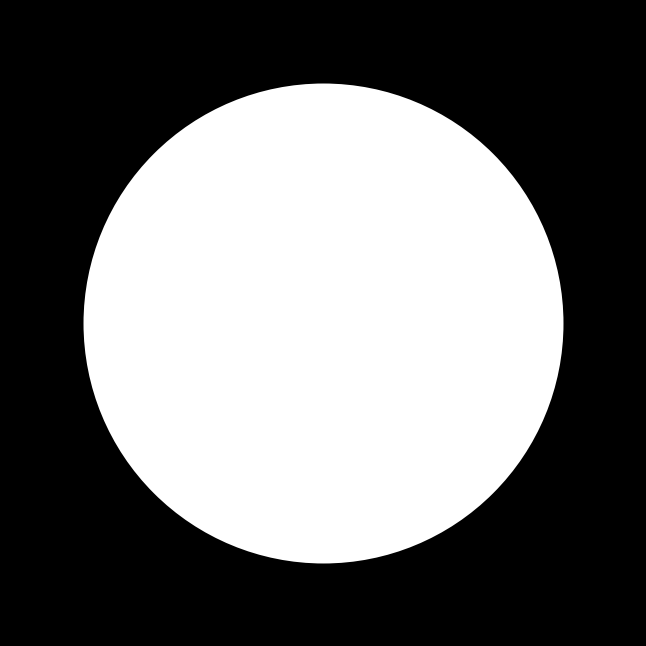

```mathematica
Graphics[{FaceForm[White], Disk[]}, Background->Black, PlotRange->{{-1.1,1.1}, {-1.1, 1.1}}]
```